```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Gaussian sensing: Kitaev chain*)

(*a1,a2,...,an,a1d,...and -> x1,x2...,xn,p1,...pn*)
QT[N1_]:=Module[{i,j,Matrix},
Matrix=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
Matrix[[i,i]]=1;
Matrix[[i,N1+i]]=1;
Matrix[[i+N1,i]]=-ⅈ;
Matrix[[i+N1,N1+i]]=ⅈ;
];
Matrix/√2
]

AMatrix[N1_,g_,ϕb_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i!=j && Abs[i-j]==1,
If[i<j,A[[i,j]]=g*Exp[-ⅈ*ϕb],
A[[i,j]]=-g*Exp[ⅈ*ϕb]
];
];
]
];
A
]

BMatrix[N1_,g_,ϕb_,χ_,ϕχ_, m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[ Abs[i-j]==1,
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
];
];
];
A
]


BosonicKitaevChain[N1_,g_,ϕb_,χ_,ϕχ_,m_]:=Module[{},
A=AMatrix[N1,g,ϕb];
B=BMatrix[N1,g,ϕb,χ,ϕχ, m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=g>=0&&χ>=0&&ϕb∈Reals&&ϕχ∈Reals;
$Assumptions=assump;
Simplify[Join[m1,m2]]
]


GenerateA[N1_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i==j,A[[i,j]]=-ⅈ*Subscript[ω, i],
If[i<j,A[[i,j]]=Subscript[g, i,j]*Exp[-ⅈ*Subscript[ϕ, b,i,j]],
A[[i,j]]=-Subscript[g, j,i]*Exp[ⅈ*Subscript[ϕ, b,j,i]]
];
];
]
];
A
]


GenerateB[N1_,m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i==j,If[m!={}&& IntersectingQ[{i},m],A[[i,j]]=Subscript[ω, i]*Exp[-ⅈ*Subscript[ϕ, s,i]],A[[i,j]]=Subscript[ξ, i]*Exp[-ⅈ*Subscript[ϕ, s,i]]]];
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=Subscript[g, i,j]*Exp[-ⅈ*Subscript[ϕ, t,i,j]],A[[i,j]]=Subscript[χ, i,j]*Exp[-ⅈ*Subscript[ϕ, t,i,j]]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=Subscript[g, j,i]*Exp[-ⅈ*Subscript[ϕ, t,j,i]],A[[i,j]]=Subscript[χ, j,i]*Exp[-ⅈ*Subscript[ϕ, t,j,i]]]];
];
];
A
]

BQH[N1_,m_]:=Module[{A,B,m1,m2,assump},
A=GenerateA[N1];
B=GenerateB[N1,m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=hui∈Reals;
For[i=1,i<=N1,i++,
assump=assump&&Subscript[ω, i]∈Reals&&Subscript[ξ, i]∈Reals&&Subscript[ϕ, s,i]∈Reals;
For[j=i,j<=N1,j++,
If[i!= j,assump=assump&&Subscript[g, i,j]∈Reals&&Subscript[χ, i,j]∈Reals&&Subscript[ϕ, t,i,j]∈Reals&&Subscript[ϕ, b,i,j]∈Reals;]
]];
$Assumptions=assump;
Simplify[Join[m1,m2]]
]

ZeroPhase[Nmodes_]:=Module[{i,j,phases},
phases={};
For[i=1,i<=Nmodes,i++,
phases=phases~Join~{Subscript[ϕ, s,i]->0};
For[j=i,j<=Nmodes,j++,
If[i!= j,phases=phases~Join~{Subscript[ϕ, t,i,j]->0,Subscript[ϕ, b,i,j]->0};]
]];
phases
]

killSPDC[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],(*kill all g_{i,j}*)Flatten@Table[Subscript[g,i,j]->0,{i,1,N1},{j,i+1,N1}],(*kill all chi except pairwise (2j-1,2j)*)Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

killSPDCBS[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[g,i,j]->g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

SPDCBS2[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1,Subscript[g,i,j]->g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

(* with a phase *)
SPDCBS3[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1,Subscript[g,i,j]->I g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->-I χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];


killomega[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}]];
killxi[N1_]:=Join[Table[Subscript[ξ,i]->0,{i,1,N1}]];
killg[N1_]:=Flatten[Table[Subscript[g,i,j]->0,{i,1,N1},{j,i+1,N1}]];
killchi[N1_]:=Flatten[Table[Subscript[χ,i,j]->0,{i,1,N1},{j,i+1,N1}]];


CovarBasis[N1_]:= Module[{i,j,A},
A=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
A[[2i-1,i]]=1;
A[[2i,N1+i]]=1
];
A]



QFIperPhoton[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]


QFIperPhotonAnal[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]

QFInoDisp[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t];
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]];
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
(1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes)/(1/4 (Tr[Σout]-2 Nmodes))//FullSimplify
]


LeadingOrderCheck[cov_,disp_,n_,Nmodes_]:=Module[{M,d,G,EOM,DM,DMq,CovForm,DispForm,nForm},
M=Nmodes;
d=Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}]//FullSimplify;
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
DMq=CovarBasis[Nmodes].DM.Transpose[CovarBasis[Nmodes]];

CovForm=Tr[1/2 1/((M-1)!)^4 MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1]]//FullSimplify;
Print["leading order covariant ",CovForm];
Print[Coefficient[cov,t^(4M-4)]==CovForm//FullSimplify];

DispForm=(2 1)/((M-1)!)^4 d.MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].d//FullSimplify;
Print["leading order displacement ",DispForm];
Print[Coefficient[disp,t^(4M-4)]==DispForm//FullSimplify];

nForm=1/(4 ((M-1)!)^2)(Tr[MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1]]+2 d.MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].d)//FullSimplify;
Print["leading order mean photon number  ",nForm];
Print[Coefficient[n,t^(2M-2)]==nForm//FullSimplify];
]


QFIperPhotonBQH[Nmodes_,EOM_]:=Module[{DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]


FnNormal[Nmodes_,g_,χ_,t_]:=Module[{},
λ=Table[2 Sqrt[χ^2-g^2] Cos[(k π)/(Nmodes+1)],{k,1,Nmodes}];
x=Table[((χ-g)/(χ+g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify,{k,1,Nmodes},{h,1,Nmodes}];
y=Table[((χ+g)/(χ-g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify,{h,1,Nmodes},{k,1,Nmodes}];
tr=Tr[(2/(Nmodes+1))^4 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{-Transpose[y].MatrixExp[-DiagonalMatrix[λ]t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ ] t].y,-x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ]t].Transpose[x]}]]]//N;

nout=1/4 Tr[(2/(Nmodes+1))^2 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x],x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x]}]]]-Nmodes/2//N;

Fcov=-1/2 tr-Nmodes;
Fcov/nout
]
```

```mathematica
Subscript[ω, 1]=.
Subscript[ξ, 1]=.
Clear[κ]
```

InterpolatingFunction[…]

1

(8 Sinh[t √(ξ_1^2-ω_1^2)]^2 ξ_1^2 (Cosh[t √(ξ_1^2-ω_1^2)]^2 ξ_1^2-ω_1^2))/((ξ_1^2-ω_1^2)^2)

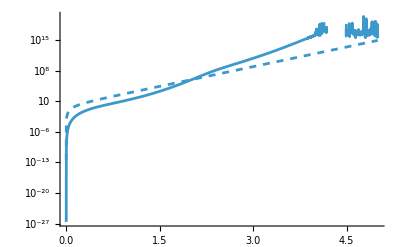

```mathematica
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];

tmax=5;
κ=0.001;Subscript[ξ, 1]=2;Subscript[ω, 1]=1;

Clear[Σin]
sol=NDSolveValue[{Σin'[t]==(DM t).Σin[t]+Σin[t].Transpose[DM t]+κ IdentityMatrix[2],Σin[0]==IdentityMatrix[2]},Σin,{t,0,tmax},AccuracyGoal->20]

G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.sol[t].Transpose[Sphase];
μsq=1/Det[Σout];
F=1/2 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]/(1+μsq);

plt1=LogPlot[{Evaluate[F/.ϕ->0]},{t,0,tmax},PlotRange->All];

(* no loss *)
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Clear[κ]

Nmodes=1;
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
μsq=1/Det[Σout]//FullSimplify

Fnoloss=1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]//FullSimplify
Subscript[ξ, 1]=2;Subscript[ω, 1]=1;
plt2=LogPlot[{Evaluate[Fnoloss/.ϕ->0]},{t,0,tmax},PlotRange->All,PlotStyle->Dashed];

Show[plt1,plt2]
```

1

(8 Sinh[t √(ξ_1^2-ω_1^2)]^2 ξ_1^2 (Cosh[t √(ξ_1^2-ω_1^2)]^2 ξ_1^2-ω_1^2))/((ξ_1^2-ω_1^2)^2)

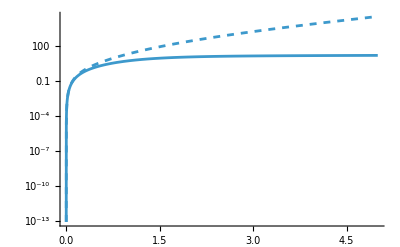

```mathematica
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];

tmax=5;
κ=1;Subscript[ξ, 1]=1.05;Subscript[ω, 1]=1;

Clear[Σin]
int=Integrate[MatrixExp[DM (t-s)] κ/2  MatrixExp[Transpose[DM] (t-s)],{s,0,t}]//FullSimplify;
S=MatrixExp[DM t];
Σin=S.Transpose[S]+int;

G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
μsq=1/Det[Σout];
F=1/2 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]/(1+μsq);

plt1=LogPlot[{Evaluate[F/.ϕ->0]},{t,0,tmax},PlotRange->All];


(* no loss *)
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Clear[κ]

Nmodes=1;
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
μsq=1/Det[Σout]//FullSimplify

Fnoloss=1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]//FullSimplify
Subscript[ξ, 1]=1.05;Subscript[ω, 1]=1;
plt2=LogPlot[{Evaluate[Fnoloss/.ϕ->0]},{t,0,tmax},PlotRange->All,PlotStyle->Dashed];

Show[plt1,plt2]
```

{{(Cosh[2 t √(ξ_1^2-ω_1^2)] ξ_1^2-ω_1^2+Sinh[2 t √(ξ_1^2-ω_1^2)] ξ_1 √(ξ_1^2-ω_1^2))/(ξ_1^2-ω_1^2),(2 Sinh[t √(ξ_1^2-ω_1^2)]^2 ξ_1 ω_1)/(-ξ_1^2+ω_1^2)},{(2 Sinh[t √(ξ_1^2-ω_1^2)]^2 ξ_1 ω_1)/(-ξ_1^2+ω_1^2),(-Cosh[2 t √(ξ_1^2-ω_1^2)] ξ_1^2+ω_1^2+Sinh[2 t √(ξ_1^2-ω_1^2)] ξ_1 √(ξ_1^2-ω_1^2))/(-ξ_1^2+ω_1^2)}}

Output covariance

((ξ_1^2 cosh(2 t √(ξ_1^2-ω_1^2))+ξ_1 √(ξ_1^2-ω_1^2) cos(2 ϕ) sinh(2 t √(ξ_1^2-ω_1^2))-ω_1 (4 ξ_1 sin(ϕ) cos(ϕ) sinh^2(t √(ξ_1^2-ω_1^2))+ω_1))/(ξ_1^2-ω_1^2) | -(2 ξ_1 (ω_1 cos(2 ϕ) sinh^2(t √(ξ_1^2-ω_1^2))+√(ξ_1^2-ω_1^2) sin(ϕ) cos(ϕ) sinh(2 t √(ξ_1^2-ω_1^2))))/(ξ_1^2-ω_1^2)
-(2 ξ_1 (ω_1 cos(2 ϕ) sinh^2(t √(ξ_1^2-ω_1^2))+√(ξ_1^2-ω_1^2) sin(ϕ) cos(ϕ) sinh(2 t √(ξ_1^2-ω_1^2))))/(ξ_1^2-ω_1^2) | (ξ_1^2 cosh(2 t √(ξ_1^2-ω_1^2))+ξ_1 (4 ω_1 sin(ϕ) cos(ϕ) sinh^2(t √(ξ_1^2-ω_1^2))-√(ξ_1^2-ω_1^2) cos(2 ϕ) sinh(2 t √(ξ_1^2-ω_1^2)))-ω_1^2)/(ξ_1^2-ω_1^2))

Purity no loss

1

(8 Sinh[t √(ξ_1^2-ω_1^2)]^2 ξ_1^2 (Cosh[t √(ξ_1^2-ω_1^2)]^2 ξ_1^2-ω_1^2))/((ξ_1^2-ω_1^2)^2)

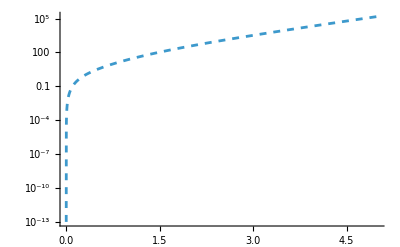

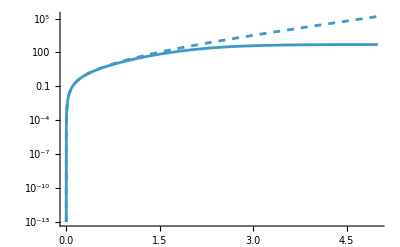

```mathematica
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];

tmax=5;
κ=.1;Subscript[ξ, 1]=1.1;Subscript[ω, 1]=1;

Clear[Σin]
int=Integrate[MatrixExp[DM (t-s)] κ  MatrixExp[Transpose[DM] (t-s)],{s,0,t}]//FullSimplify;
S=MatrixExp[DM t];
Σin=S.Transpose[S]+int;

G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
μsq=1/Det[Σout];
F=1/2 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]/(1+μsq);

plt1=LogPlot[{Evaluate[F/.ϕ->0]},{t,0,tmax},PlotRange->All];


(* no loss *)
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Clear[κ]

Nmodes=1;
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
"Output covariance"
Σout//TraditionalForm

"Purity no loss"
μsq=1/Det[Σout]//FullSimplify

Fnoloss=1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]//FullSimplify
Subscript[ξ, 1]=1.1;Subscript[ω, 1]=1;
plt2=LogPlot[{Evaluate[Fnoloss/.ϕ->0]},{t,0,tmax},PlotRange->All,PlotStyle->Dashed]

Show[plt1,plt2]
```

DM is

(0 | 1
-1 | -2)

{{3+ⅇ^(-2 t) (-3-2 t (2+t)),-1+ⅇ^(-2 t) (1+2 t (1+t))},{-1+ⅇ^(-2 t) (1+2 t (1+t)),1-ⅇ^(-2 t) (1+2 t^2)}}

(8 (1+ⅇ^(4 t)-2 ⅇ^(2 t) (1+t)+2 t (1+t)))/(-1+3 ⅇ^(4 t)-4 ⅇ^(2 t) t)

QFI limit

2.66667

Mean photon limit

0.5

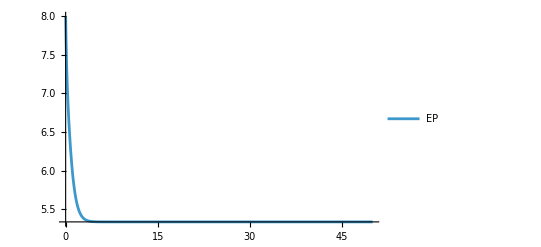

{{10.6452-0.241513 ⅇ^(-3.66132 t)+1.44928 ⅇ^(-2. t)-11.8529 ⅇ^(-0.338675 t),-4.19355+0.514584 ⅇ^(-3.66132 t)-1.88406 ⅇ^(-2. t)+5.56302 ⅇ^(-0.338675 t)},{-4.19355+0.514584 ⅇ^(-3.66132 t)-1.88406 ⅇ^(-2. t)+5.56302 ⅇ^(-0.338675 t),2.25806-1.0964 ⅇ^(-3.66132 t)+1.44928 ⅇ^(-2. t)-2.61094 ⅇ^(-0.338675 t)}}

2.72581

Mean photon limit

2.72581

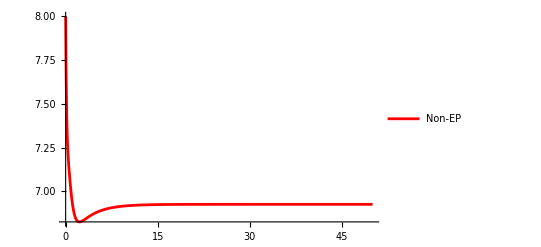

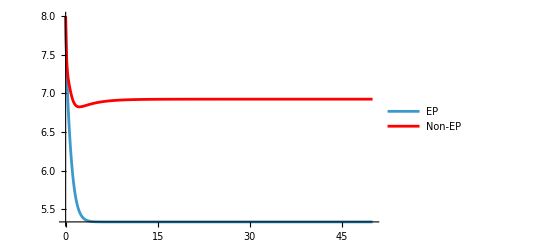

```mathematica
Clear[κ]
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Subscript[ξ, 1]=1;
Subscript[ω, 1]=1;
κ=2;

Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
"DM is"
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
DM//MatrixForm

tmax=50;


Clear[Σin]
int=Integrate[κ  MatrixExp[DM (t-s)].MatrixExp[Transpose[DM] (t-s)],{s,0,t}]//FullSimplify
S=MatrixExp[DM t];
Σin=S.Transpose[S]+int;
n=1/4 (Tr[Σin]-2 Nmodes)//FullSimplify;

G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
μsq=1/Det[Σout];

F=1/2 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]/(1+μsq)//FullSimplify
"QFI limit"
Limit[F,t->∞]//N
"Mean photon limit"
Limit[n,t->∞]//N

plt1=Plot[{Evaluate[F/.ϕ->0]/n},{t,0,tmax},PlotRange->All,PlotLegends->{"EP"}]


Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Subscript[ξ, 1]=1.3;
Subscript[ω, 1]=1;

Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];



Clear[Σin]
int=Integrate[κ  MatrixExp[DM (t-s)].MatrixExp[Transpose[DM] (t-s)],{s,0,t}]//FullSimplify//Chop
Limit[1/4 Tr[int]-Nmodes/2,t->∞]
S=MatrixExp[DM t];
Σin=S.Transpose[S]+int;
n=1/4 (Tr[Σin]-2 Nmodes)//FullSimplify;

G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
μsq=1/Det[Σout];

F=1/2 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]/(1+μsq);

"Mean photon limit"
Limit[n,t->∞]//N


plt2=Plot[{Evaluate[F/.ϕ->0]/n},{t,0,tmax},PlotRange->All, PlotStyle->Red,PlotLegends->{"Non-EP"}]


Show[plt1,plt2]
```

```mathematica
(* steady-state analytical *)
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Clear[κ]
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
EOM//MatrixForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
DM//FullSimplify//MatrixForm
DM//Eigenvalues//FullSimplify
"SS covariance matrix"
Σin=LyapunovSolve[DM ,Transpose[DM],-κ IdentityMatrix[2]]//FullSimplify;
Σin//MatrixForm


G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
"Purity"
μsq=1/Det[Σout]//FullSimplify

F=1/2 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]/(1+μsq)//FullSimplify
n=1/4 (Tr[Σin]-2 Nmodes)//FullSimplify

"QFI normalized to mean"
F/n//FullSimplify

"EP"
F/n/.Subscript[ξ, 1]->1/.κ->2/.Subscript[ω, 1]->1//N
F/.{Subscript[ξ, 1]->1,κ->2,Subscript[ω, 1]->1}//N
n/.{Subscript[ξ, 1]->1,κ->2,Subscript[ω, 1]->1}//N
Σin/.{Subscript[ξ, 1]->1,κ->2,Subscript[ω, 1]->1}//MatrixForm
Eigensystem[DM/.{Subscript[ξ, 1]->1,κ->2,Subscript[ω, 1]->1}]

"Above EP"
F/n/.Subscript[ξ, 1]->1.3/.κ->2/.Subscript[ω, 1]->1//N
F/.{Subscript[ξ, 1]->1.3,κ->2,Subscript[ω, 1]->1}
n/.{Subscript[ξ, 1]->1.3,κ->2,Subscript[ω, 1]->1}
Eigensystem[DM/.{Subscript[ξ, 1]->1.3,κ->2,Subscript[ω, 1]->1}]


"At Threshold"
F/n/.Subscript[ξ, 1]->Sqrt[Subscript[ω, 1]^2+1]-0.001/.κ->2/.Subscript[ω, 1]->1//N
F/.Subscript[ξ, 1]->Sqrt[Subscript[ω, 1]^2+1]-0.001/.κ->2/.Subscript[ω, 1]->1
n/.Subscript[ξ, 1]->Sqrt[Subscript[ω, 1]^2+1]-0.001/.κ->2/.Subscript[ω, 1]->1
Eigensystem[DM/.Subscript[ξ, 1]->Sqrt[Subscript[ω, 1]^2+1]-0.001/.κ->2/.Subscript[ω, 1]->1]
```

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

(-κ/2-ⅈ ω_1 | ξ_1
ξ_1 | -κ/2+ⅈ ω_1)

(-κ/2+ξ_1 | ω_1
-ω_1 | -κ/2-ξ_1)

{-κ/2-√(ξ_1^2-ω_1^2),-κ/2+√(ξ_1^2-ω_1^2)}

SS covariance matrix

(1+(2 ξ_1 (κ+2 ξ_1))/(κ^2-4 ξ_1^2+4 ω_1^2) | -(4 ξ_1 ω_1)/(κ^2-4 ξ_1^2+4 ω_1^2)
-(4 ξ_1 ω_1)/(κ^2-4 ξ_1^2+4 ω_1^2) | (κ^2-2 κ ξ_1+4 ω_1^2)/(κ^2-4 ξ_1^2+4 ω_1^2))

Purity

1-(4 ξ_1^2)/(κ^2+4 ω_1^2)

(8 ξ_1^2 (κ^2+4 ω_1^2))/(8 ξ_1^4-6 ξ_1^2 (κ^2+4 ω_1^2)+(κ^2+4 ω_1^2)^2)

(2 ξ_1^2)/(κ^2-4 ξ_1^2+4 ω_1^2)

QFI normalized to mean

4+(8 ξ_1^2)/(κ^2-2 ξ_1^2+4 ω_1^2)

EP

5.33333

2.66667

0.5

(3 | -1
-1 | 1)

{{-1,-1},{{-1,1},{0,0}}}

Above EP

6.92641

18.88

2.72581

{{-1.83066,-0.169338},{{-0.42487+0. ⅈ,0.905254+0. ⅈ},{0.905254+0. ⅈ,-0.42487+0. ⅈ}}}

At Threshold

7.98871

2821.44

353.178

{{-1.99859,-0.00141471},{{-0.38301+0. ⅈ,0.923744+0. ⅈ},{0.923744+0. ⅈ,-0.38301+0. ⅈ}}}

```mathematica
Eigensystem[DM]/.Subscript[ξ, 1]->Subscript[ω, 1]
Eigensystem[DM]
```

{{-1,-1},{{-1,1},{-1,1}}}

{{-1-√(ξ_1^2-ω_1^2),-1+√(ξ_1^2-ω_1^2)},{{-(ξ_1-√(ξ_1^2-ω_1^2))/ω_1,1},{-(ξ_1+√(ξ_1^2-ω_1^2))/ω_1,1}}}

```mathematica
κ=2;
Solve[κ^2-2 Subscript[ξ, 1]^2+4 Subscript[ω, 1]^2==0]//FullSimplify
```

{{ω_1→ConditionalExpression[-(√(-2+ξ_1^2))/(√2), ξ_1≥√2||√2+ξ_1≤0]},{ω_1→ConditionalExpression[(√(-2+ξ_1^2))/(√2), ξ_1≥√2||√2+ξ_1≤0]}}

```mathematica
4+(8 Subscript[ξ, 1]^2)/(κ^2-2 Subscript[ξ, 1]^2+4 Subscript[ω, 1]^2)/.Subscript[ω, 1]->Sqrt[Subscript[ξ, 1]^2-1]//FullSimplify
```

8-(4 (-4+κ^2))/(-4+κ^2+2 ξ_1^2)

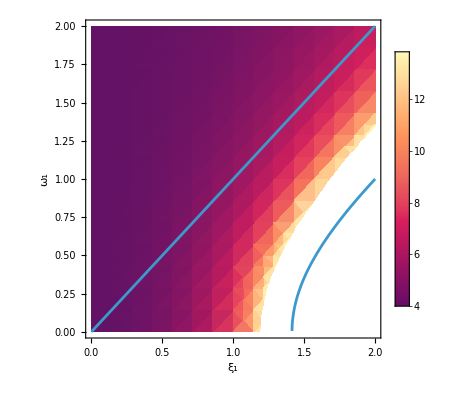

```mathematica
κ=2;

Show[DensityPlot[4+(8 Subscript[ξ, 1]^2)/(κ^2-2 Subscript[ξ, 1]^2+4 Subscript[ω, 1]^2),{Subscript[ξ, 1],0,2},{Subscript[ω, 1],0,2},PlotLegends->Automatic,FrameLabel->{"ξ_1","ω_1"},Exclusions->Automatic],Plot[(√(-2+Subscript[ξ, 1]^2))/(√2),{Subscript[ξ, 1],0,2},AspectRatio->1,PlotRange->{0,2}],Plot[Subscript[ξ, 1],{Subscript[ξ, 1],0,2},AspectRatio->1]]
```

```mathematica
Subscript[ξ, 1]=1;
Subscript[ω, 1]=1;
κ=2;

σt[t_]:=Module[{s},Integrate[MatrixExp[DM (t-s)] κ IdentityMatrix[2] MatrixExp[Transpose[DM] (t-s)],{s,0,t}]];
σt[200]//Chop//N

Integrate[κ MatrixExp[DM (t-s)].MatrixExp[Transpose[DM] (t-s)],{s,0,t}]/.t->200//N
```

{{2.5,0.},{0.,0.5}}

{{3.,-1.},{-1.,1.}}

```mathematica
(* steady state *)
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Subscript[ξ, 1]=1.3;
Subscript[ω, 1]=1;
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
EOM//MatrixForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
DM//FullSimplify//MatrixForm
Σin=LyapunovSolve[DM ,Transpose[DM],-κ IdentityMatrix[2]]//FullSimplify
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify
μsq=1/Det[Σout]//FullSimplify
F=1/2 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]/(1+μsq)//FullSimplify//Chop


Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Subscript[ξ, 1]=1;
Subscript[ω, 1]=1;
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
EOM//MatrixForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
DM//FullSimplify//MatrixForm
Σin=LyapunovSolve[DM ,Transpose[DM],-κ IdentityMatrix[2]]//FullSimplify
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify
μsq=1/Det[Σout]//FullSimplify
F=1/2 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]/(1+μsq)//FullSimplify//N
```

(-1-ⅈ | 1.3
1.3 | -1+ⅈ)

(0.3+0. ⅈ | 1.+0. ⅈ
-1.+0. ⅈ | -2.3+0. ⅈ)

{{10.6452+0. ⅈ,-4.19355+0. ⅈ},{-4.19355+0. ⅈ,2.25806+0. ⅈ}}

{{6.45161+4.19355 Cos[2 ϕ]-8.3871 Cos[ϕ] Sin[ϕ],-4.19355 Cos[2 ϕ]-8.3871 Cos[ϕ] Sin[ϕ]},{-4.19355 Cos[2 ϕ]-8.3871 Cos[ϕ] Sin[ϕ],6.45161-4.19355 Cos[2 ϕ]+8.3871 Cos[ϕ] Sin[ϕ]}}

0.155

18.88

(-1-ⅈ | 1
1 | -1+ⅈ)

(0 | 1
-1 | -2)

{{3,-1},{-1,1}}

{{2+Cos[2 ϕ]-Sin[2 ϕ],-Cos[2 ϕ]-Sin[2 ϕ]},{-Cos[2 ϕ]-Sin[2 ϕ],2-Cos[2 ϕ]+Sin[2 ϕ]}}

1/2

2.66667

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

{{-1-ⅈ ω_1,ξ_1},{ξ_1,-1+ⅈ ω_1}}

{{-1+ξ_1,ω_1},{-ω_1,-1-ξ_1}}

{{-1,-1},{{-ⅈ,1},{0,0}}}

{{-1-√(ξ_1^2-ω_1^2),-1+√(ξ_1^2-ω_1^2)},{{-(ⅈ ω_1+√(ξ_1^2-ω_1^2))/ξ_1,1},{(-ⅈ ω_1+√(ξ_1^2-ω_1^2))/ξ_1,1}}}

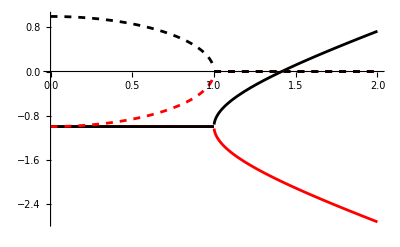

{{-1,-1},{{-ⅈ,1},{0,0}}}

{{-1.9798,-0.0202041},{{-0.494872-0.505076 ⅈ,0.707107},{0.494872-0.505076 ⅈ,0.707107}}}

```mathematica
Nmodes=1;
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Clear[κ]
κ=2;
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes]
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]]//FullSimplify

Eigensystem[EOM/.Subscript[ξ, 1]->Subscript[ω, 1]]
eig=Eigensystem[EOM]//FullSimplify

Plot[Evaluate[{Re[eig[[1,1]]],Re[eig[[1,2]]],Im[eig[[1,1]]],Im[eig[[1,2]]]}/.Subscript[ω, 1]->1],{Subscript[ξ, 1],0,2},PlotStyle->{Red,Black,{Red,Dashed},{Black,Dashed}}]

Eigensystem[EOM/.Subscript[ξ, 1]->1/.Subscript[ω, 1]->1]
Eigensystem[EOM/.Subscript[ξ, 1]->1.4/.Subscript[ω, 1]->1]//Chop
```

(-κ/2-ⅈ ω_1 | ξ_1
ξ_1 | -κ/2+ⅈ ω_1)

(-κ/2+ξ_1 | ω_1
-ω_1 | -κ/2-ξ_1)

{{-(-κ^2-2 κ ξ_1-4 ω_1^2)/(2 t (κ^2-4 ξ_1^2+4 ω_1^2)),-(2 ξ_1 ω_1)/(t (κ^2-4 ξ_1^2+4 ω_1^2))},{-(2 ξ_1 ω_1)/(t (κ^2-4 ξ_1^2+4 ω_1^2)),-(-κ^2+2 κ ξ_1-4 ω_1^2)/(2 t (κ^2-4 ξ_1^2+4 ω_1^2))}}

{{(κ^2+2 κ Cos[2 ϕ] ξ_1-4 Sin[2 ϕ] ξ_1 ω_1+4 ω_1^2)/(2 t κ^2-8 t ξ_1^2+8 t ω_1^2),-(ξ_1 (κ Sin[2 ϕ]+2 Cos[2 ϕ] ω_1))/(t (κ^2-4 ξ_1^2+4 ω_1^2))},{-(ξ_1 (κ Sin[2 ϕ]+2 Cos[2 ϕ] ω_1))/(t (κ^2-4 ξ_1^2+4 ω_1^2)),(κ^2-2 κ Cos[2 ϕ] ξ_1+4 Sin[2 ϕ] ξ_1 ω_1+4 ω_1^2)/(2 t κ^2-8 t ξ_1^2+8 t ω_1^2)}}

4 t^2 (1-(4 ξ_1^2)/(κ^2+4 ω_1^2))

(16 ξ_1^2 (κ^2+4 ω_1^2))/((κ^2-4 ξ_1^2+4 ω_1^2) (-16 t^2 ξ_1^2+(1+4 t^2) (κ^2+4 ω_1^2)))

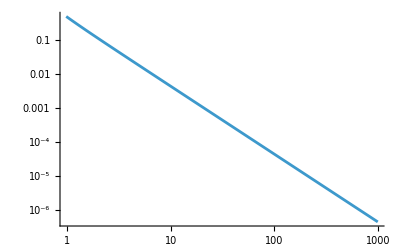

```mathematica
(* steady state *)
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Clear[κ]
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
EOM//MatrixForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
DM//FullSimplify//MatrixForm
Σin=LyapunovSolve[DM t,Transpose[DM t],-κ/2 IdentityMatrix[2]]
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify
μsq=1/Det[Σout]//FullSimplify
F=1/2 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]]/(1+μsq)//FullSimplify
LogLogPlot[F/.{Subscript[ω, 1]->1,Subscript[ξ, 1]->2,κ->.001},{t,0,1000},PlotRange->All]
```

```mathematica
Ω={{0,1},{-1,0}};
c=Sqrt[κ] IdentityMatrix[2];
(Ω.c.Ω.Transpose[c])/2
Ω.c.Transpose[c].Transpose[Ω]
Ω.c
```

{{-κ/2,0},{0,-κ/2}}

{{κ,0},{0,κ}}

{{0,√κ},{-√κ,0}}

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

{{-1/2-ⅈ ω_1,ξ_1},{ξ_1,-1/2+ⅈ ω_1}}

{{-1/2+ξ_1,ω_1},{-ω_1,-1/2-ξ_1}}

{{-1/2,-1/2},{{-ⅈ,1},{0,0}}}

{{-1/2-√(ξ_1^2-ω_1^2),-1/2+√(ξ_1^2-ω_1^2)},{{-(ⅈ ω_1+√(ξ_1^2-ω_1^2))/ξ_1,1},{(-ⅈ ω_1+√(ξ_1^2-ω_1^2))/ξ_1,1}}}

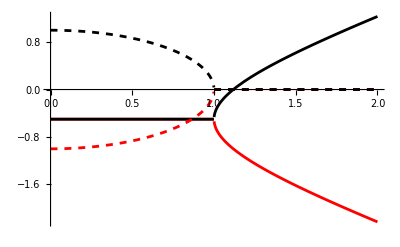

{{-1/2-√(1-ω_1^2),-1/2+√(1-ω_1^2)},{{-ⅈ ω_1-√(1-ω_1^2),1},{-ⅈ ω_1+√(1-ω_1^2),1}}}

```mathematica
Nmodes=1;
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Clear[κ]
κ=1;
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes]
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]]//FullSimplify

Eigensystem[EOM/.Subscript[ξ, 1]->Subscript[ω, 1]]
eig=Eigensystem[EOM]//FullSimplify

Plot[Evaluate[{Re[eig[[1,1]]],Re[eig[[1,2]]],Im[eig[[1,1]]],Im[eig[[1,2]]]}/.Subscript[ω, 1]->1],{Subscript[ξ, 1],0,2},PlotStyle->{Red,Black,{Red,Dashed},{Black,Dashed}}]

eig/.Subscript[ξ, 1]->1
```

```mathematica
$Assumptions={Subscript[ω, 1],Subscript[ξ, 1],κ}∈Reals;
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
EOM//MatrixForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]]//FullSimplify;
DM//MatrixForm

int=Integrate[MatrixExp[DM (t-s)] κ/2  MatrixExp[Transpose[DM] (t-s)],{s,0,t}]//FullSimplify;
S=MatrixExp[DM t];
Σin=S.Transpose[S]+int;

G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];

Ω={{0,1},{-1,0}};
Fcov=1/2 Flatten[D[Σout,ϕ]].Inverse[KroneckerProduct[Σout,Σout]+(1/4) KroneckerProduct[Ω,Ω]].Flatten[D[Σout,ϕ]]/.ϕ->0;
```

(-κ/2-ⅈ ω_1 | ξ_1
ξ_1 | -κ/2+ⅈ ω_1)

(-κ/2+ξ_1 | ω_1
-ω_1 | -κ/2-ξ_1)

https://indico.ictp.it/event/9021/session/10/contribution/41/material/slides/0.pdf

```mathematica
Σin=LyapunovSolve[DM t,Transpose[DM t],κ/2 IdentityMatrix[2]]
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify
Ω={{0,1},{-1,0}};
Fcov=1/2 Flatten[D[Σout,ϕ]].Inverse[KroneckerProduct[Σout,Σout]+(1/4) KroneckerProduct[Ω,Ω]].Flatten[D[Σout,ϕ]]//FullSimplify
```

{{-(κ^2+2 κ ξ_1+4 ω_1^2)/(2 t (κ^2-4 ξ_1^2+4 ω_1^2)),(2 ξ_1 ω_1)/(t (κ^2-4 ξ_1^2+4 ω_1^2))},{(2 ξ_1 ω_1)/(t (κ^2-4 ξ_1^2+4 ω_1^2)),-(κ^2-2 κ ξ_1+4 ω_1^2)/(2 t (κ^2-4 ξ_1^2+4 ω_1^2))}}

{{-(κ^2+4 ω_1^2+2 ξ_1 (κ Cos[2 ϕ]-2 Sin[2 ϕ] ω_1))/(2 t (κ^2-4 ξ_1^2+4 ω_1^2)),(ξ_1 (κ Sin[2 ϕ]+2 Cos[2 ϕ] ω_1))/(t (κ^2-4 ξ_1^2+4 ω_1^2))},{(ξ_1 (κ Sin[2 ϕ]+2 Cos[2 ϕ] ω_1))/(t (κ^2-4 ξ_1^2+4 ω_1^2)),-(κ^2+4 ω_1^2+ξ_1 (-2 κ Cos[2 ϕ]+4 Sin[2 ϕ] ω_1))/(2 t (κ^2-4 ξ_1^2+4 ω_1^2))}}

-(16 ξ_1^2 (κ^2+4 ω_1^2))/((κ^2-4 ξ_1^2+4 ω_1^2) (-4 t^2 ξ_1^2+(-1+t^2) (κ^2+4 ω_1^2)))

```mathematica
EOM2=BQH[Nmodes,{}]/.ZeroPhase[Nmodes];
{F2,d2,n2}=QFIperPhotonBQH[Nmodes,EOM2]//FullSimplify
```

{(8 Sinh[t √(ξ_1^2-ω_1^2)]^2 ξ_1^2 (Cosh[t √(ξ_1^2-ω_1^2)]^2 ξ_1^2-ω_1^2))/((ξ_1^2-ω_1^2)^2),1/((ξ_1^2-ω_1^2)^2)2 ((p1^2+x1^2) Cosh[4 t √(ξ_1^2-ω_1^2)] ξ_1^4-2 (p1^2+x1^2) (-1+2 Cosh[2 t √(ξ_1^2-ω_1^2)]) ξ_1^2 ω_1^2+(p1^2+x1^2) ω_1^4+2 ξ_1 ω_1^2 (-4 p1 x1 Sinh[t √(ξ_1^2-ω_1^2)]^2 ω_1+(p1-x1) (p1+x1) Sinh[2 t √(ξ_1^2-ω_1^2)] √(ξ_1^2-ω_1^2))+ξ_1^3 (8 p1 x1 Cosh[2 t √(ξ_1^2-ω_1^2)] Sinh[t √(ξ_1^2-ω_1^2)]^2 ω_1+(-p1^2+x1^2) Sinh[4 t √(ξ_1^2-ω_1^2)] √(ξ_1^2-ω_1^2))),((-1+(1+p1^2+x1^2) Cosh[2 t √(ξ_1^2-ω_1^2)]) ξ_1^2-(p1^2+x1^2) ω_1^2+ξ_1 (4 p1 x1 Sinh[t √(ξ_1^2-ω_1^2)]^2 ω_1+(-p1^2+x1^2) Sinh[2 t √(ξ_1^2-ω_1^2)] √(ξ_1^2-ω_1^2)))/(2 (ξ_1^2-ω_1^2))}

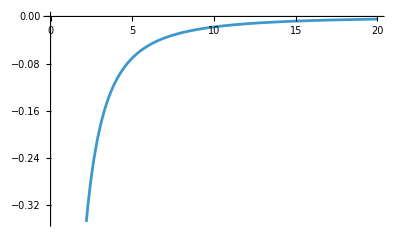

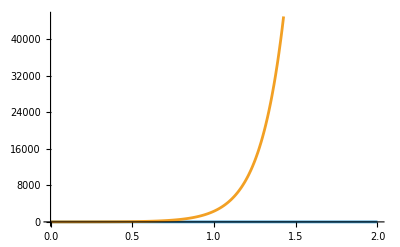

```mathematica
Subscript[ω, 1]=1;
Subscript[ξ, 1]=2;
κ=0.1;
Plot[{Fcov},{t,0,20}]
```

```mathematica
σ[t_]:={{σ11[t],σ12[t]},{σ21[t],σ22[t]}};

eqs=Thread[D[σ[t],t]==DM.σ[t]+σ[t].Transpose[DM]+κ/2 IdentityMatrix[2]];

conds=Thread[σ[0]==IdentityMatrix[2]];

Subscript[ω, 1]=1;Subscript[ξ, 1]=0.1;κ=0.1;
sol=NDSolveValue[{eqs,conds},σ[t],{t,0.1,1}];
σloss=sol[1]
(*covariance at time tstar*)
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}[1]